```mathematica
P=DiscreteMarkovProcess[{1,0,0,0},{{0,1/2,1/2,0},{1/2,0,1/3,1/6},{1/4,1/4,1/4,1/4},{1/2,0,0,1/2}}];
```

```mathematica
StationaryDistribution[P]
```

ProbabilityDistribution[2/7 Boole[x==1]+3/14 Boole[x==2]+2/7 Boole[x==3]+3/14 Boole[x==4],{x,1,4,1}]

```mathematica
data=Normal[RandomFunction[P,{0,10000}]][[1]][[All,2]];
```

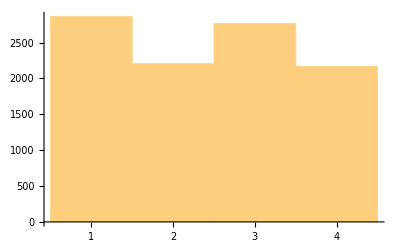

```mathematica
Histogram[data]
```

```mathematica
P1=DiscreteMarkovProcess[{1,0,0,0},{{0,1/2,1/2,0},{1/2,0,1/3,1/6},{1/4,1/4,1/4,1/4},{1/2,0,1/6,1/3}}];
```

```mathematica
StationaryDistribution[P1]
```

ProbabilityDistribution[19/68 Boole[x==1]+15/68 Boole[x==2]+11/34 Boole[x==3]+3/17 Boole[x==4],{x,1,4,1}]

```mathematica
data=Normal[RandomFunction[P1,{0,10000}]][[1]][[All,2]];
```

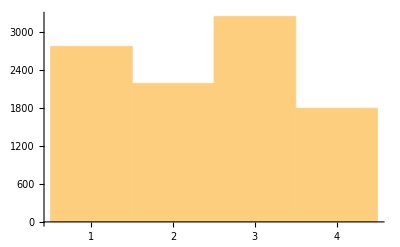

```mathematica
Histogram[data]
```